-Graphics-

# Structured Data

-Graphics-

## Learning Objectives

The following types of structured data will be described:

List

PackedArray

SparseArray

Association

Each of the following sections will explain how and when a data type should be used.

## List ({...})

Lists are general objects that represent collections of arbitrary expressions. They work best when the length of the collection rarely changes.

Here is an example of a basic list:

```mathematica
list = List[a, b, c, d]
```

Notice that the input was entered using the verbose FullForm version of List, but the output was given using the short form with brackets. Typically, the short form is used for input as well:

```mathematica
list = {a, b, c, d}
```

The output is the same. It is always possible to see the FullForm of an expression:

```mathematica
FullForm[list]
```

The elements of a list can contain any Wolfram Language expression:

```mathematica
{x, Region@Cone[], Plot[Sin[x], {x, 0, 2Pi}]}
```

In particular, an element of a list can be another list. This is how matrices are constructed:

```mathematica
matrix = {{a, b}, {c, d}}
```

Use MatrixForm to view the nested list object as a matrix:

```mathematica
x = matrix//MatrixForm
```

Note that  MatrixForm is only an output style.

```mathematica
matrix.matrix
x.x
```

## List: Element Extraction

### Part ([[...]])

#### FullForm

The most common method to extract parts of a list is to use Part, which has the short form [[ ]]. For example, given this list:

```mathematica
list = {1,2,3,4,5,6,7,8,9,10};
```

The second element of the list can be obtained with:

```mathematica
Part[list, 2]
```

The previous example used the FullForm of Part, but it is much more convenient and readable to use the short form with brackets:

```mathematica
list[[2]]
```

It is also possible to use special characters instead of double brackets:

```mathematica
list⟦2⟧
```

This last version is nice because it distinguishes the double brackets for Part from nested function calls like f[g[x]], so it will be used in the remainder of this talk.

#### Part specifications

When a positive index is used in Part, the count starts from the beginning. It is also possible to specify the part using a negative index, in which case the count starts at the end of the list. For example, here is the second-to-last element:

```mathematica
list⟦-2⟧
```

To obtain multiple parts, use a list as the argument:

```mathematica
list⟦{1, 3}⟧
```

Another very useful part specification is Span, with the short form ;;. The following Span specification takes the second through the sixth elements in steps of 2:

```mathematica
Span[2,6,2]
```

Using Span in a Part specification:

```mathematica
{1,2,3,4,5,6,7,8}⟦2;;6;;2⟧
```

Finally, it is possible to use UpTo in a span specification. Typically, when specifying an index that is out of range (e.g., an index that is longer than the length of the list), you will get an error:

```mathematica
{1,2,3,4,5,6,7,8}⟦2;;10⟧
```

Using UpTo allows the specification of a span that would be out of range:

```mathematica
{1,2,3,4,5,6,7,8}⟦2;;UpTo[10]⟧
```

#### Nested part specifications

For nested lists (e.g., a matrix), you can use Part to extract a nested part (or list of parts). Here is a matrix:

```mathematica
matrix = {{a,b,c},{d,e,f},{g,h,i}};
matrix //MatrixForm
```

To get the second element of the third list (row):

```mathematica
matrix⟦3,2⟧
```

In this case, it is also possible to nest Part specifications to obtain the same answer:

```mathematica
matrix⟦3⟧⟦2⟧
```

Get the second column:

```mathematica
matrix⟦All,2⟧
```

Get a submatrix:

```mathematica
matrix⟦{1,3},{1,3}⟧
```

### Extract/Take

It is possible to use Extract and Take as well to extract parts from a list.

```mathematica
Extract[list, 2]
```

```mathematica
Extract[matrix,{3,2}]
```

```mathematica
Extract[matrix,{All,2}]
```

```mathematica
Take[list, 2]
```

```mathematica
Take[list, {2,6}]
```

```mathematica
Take[matrix,2]
```

```mathematica
Take[matrix,All,2]
```

### Pitfalls

Nested Part specifications are not always equivalent to a single Part specification. For example:

```mathematica
matrix⟦{1,3}, 2⟧
matrix⟦{1,3}⟧⟦2⟧
```

Extract and Take are not the same as Part. In particular, Extract interprets nested lists of indices as a request to extract multiple parts. For example:

```mathematica
Extract[matrix,{{1,3},{1,3}}]
```

```mathematica
Take[matrix,{1,3},{1,3}]
```

## List: Modification

#### Part

In the previous slide, Part was used to obtain parts of a list. It is also possible to use Part on the left-hand side of a Set operation:

```mathematica
list
```

```mathematica
list⟦5⟧=X;
list
```

```mathematica
matrix//MatrixForm
```

```mathematica
matrix⟦2,2⟧=Region@Cone[];
matrix //MatrixForm
```

Just like before, it is also possible to use a list to modify multiple values.

Setting all of the elements to a single value:

```mathematica
list⟦{1,5}⟧=y;
list
```

Setting each element to a different value :

```mathematica
list⟦{2,6}⟧={Pi, E};
list
```

Finally, you can also use Span, as before:

```mathematica
matrix⟦All, 2⟧={10,100,1000};
matrix //MatrixForm
```

#### ReplacePart

ReplacePart can also be used to create a new list with parts that have been modified:

```mathematica
ReplacePart[list, 5->"NEW"]
```

Notice that list has not been modified:

```mathematica
list
```

#### Join, Flatten, Append

Use Join to join lists together:

```mathematica
list1 = {a, b, c};
list2 = {d, e, f};
Join[list1, list2]
```

Here are two matrices:

```mathematica
(matrix1 = {{1,2},{3,4}})//MatrixForm
(matrix2 = {{a,b},{c,d}})//MatrixForm
```

The default level specification stacks the two matrices on top of each other:

```mathematica
Join[matrix1, matrix2]//MatrixForm
```

Using a level specification of 2 joins the two matrices side by side:

```mathematica
Join[matrix1, matrix2, 2]//MatrixForm
```

It is also possible to use Append/Prepend to increase or decrease the size of a list:

```mathematica
Append[matrix1, x]
```

Flatten can be used to convert a nested list into an unnested list:

```mathematica
Flatten[matrix1]
```

An interesting application of Flatten is to transpose an array. For example:

```mathematica
matrix1//MatrixForm
Flatten[matrix1,{{2},{1}}]//MatrixForm
```

#### Partition, ArrayReshape

Partition and ArrayReshape comes handy if you need to change the structure of your list

```mathematica
Partition[{a,b,c,d,e,f},2]
```

Partition into sublists of length 3 with offset 1:

```mathematica
Partition[{a,b,c,d,e,f},3,1]
```

Specify the desired dimensions:

```mathematica
ArrayReshape[Range[24],{2,3,4}]
```

Use a constant padding value:

```mathematica
ArrayReshape[{1,2,3,4,5,6,7},{5,3},x]
```

{{1,2,3},{4,5,6},{7,x,x},{x,x,x},{x,x,x}}

## List: Construction

#### Table

Table is the basic tool to create a list:

```mathematica
Table[i^2, {i, 10}]
```

Create a matrix:

```mathematica
Table[i j, {i, 3}, {j, 3}]//MatrixForm
```

Use a list iterator:

```mathematica
Table[i+1, {i, {1,17,3,4,18}}]
```

#### Range

Range is basically a specialized Table idiom for creating an arithmetic progression:

```mathematica
Range[10]
Range[5,11]
Range[10,6,-1]
```

#### Array

Array can be used to generate an array with a function f applied to the indices:

```mathematica
Array[f, 5]
```

It is convenient for creating a symbolic matrix:

```mathematica
Array[Subscript[m,##]&, {3,3}]//MatrixForm
```

#### ConstantArray

Use ConstantArray to create an array where every element is the same:

```mathematica
ConstantArray[1, {3,3}]
```

Of course, it is also possible to use Table, although the syntax is slightly different:

```mathematica
Table[1, {3},{3}]
```

## List: Listability

One of the nice features of lists is that operations on lists typically occur elementwise. For example:

```mathematica
list = {1, 2,3};
list+1
```

This is much more convenient than doing something like:

```mathematica
Table[list⟦i⟧+1, {i, 3}]
```

Other examples:

```mathematica
Sin[{1.,2.,.3}]
```

```mathematica
list^2+list
```

As will be demonstrated in the next topic, operations on entire lists in this manner not only produce more readable code, they can be much faster.

## List: Performance Considerations

Copying or creating lists has a timing that is linear in the length of the list. This means that creating a list by repeatedly appending elements actually has a timing that is quadratic in the length of the list:

```mathematica
makeList[n_] := Module[{tmp={}},
	Do[AppendTo[tmp, i], {i, n}];
	tmp
]
```

The preceding function just creates a list of integers:

```mathematica
makeList[10]
```

A comparison of the timing complexity of makeList with Range:

```mathematica
Needs["GeneralUtilities`"]
BenchmarkPlot[{Range,makeList}, Identity,"IncludeFits"->True]
```

-Graphics-

Later, Association will be introduced, which has a timing complexity logarithmic in the length of the list for this kind of operation.

An alternative to using an append operation is to preallocate an array, and then to use in-place modification to update the values. This is because in-place modification does not create a copy of the array:

```mathematica
inPlace[n_]:=Module[{tmp=ConstantArray[0, n]},
Do[tmp⟦i⟧=i, {i, n}];
tmp
]
```

Example output:

```mathematica
inPlace[10]
```

Benchmark:

```mathematica
Needs["GeneralUtilities`"]
BenchmarkPlot[{Range,inPlace}, Identity,"IncludeFits"->True]
```

-Graphics-

## List: Summary

General container for arbitrary expressions.

Optimal when size of list does not change.

## PackedArray

The basic List structure described has a memory footprint quite a bit larger than what you might expect based on the size of the data structure in a language like C. For this reason, packed arrays were introduced into the language when the elements of the array all have the same type, with supported types being Integer, Real and Complex. To work with packed arrays, it will be convenient to load the Developer utilities package:

```mathematica
Needs["Developer`"]
```

## PackedArray: Memory

An example of a packed array (generated automatically by RandomReal) and the corresponding unpacked array:

Reals:

```mathematica
packedRealArray = RandomReal[1, 10^6];
unpackedRealArray = FromPackedArray @ packedRealArray;
```

Integers:

```mathematica
packedIntegerArray = RandomInteger[1, 10^6];
unpackedIntegerArray = FromPackedArray @ packedIntegerArray;
```

Complex numbers:

```mathematica
packedComplexArray = RandomComplex[1+I, 10^6];
unpackedComplexArray = FromPackedArray @ packedComplexArray;
```

Comparison of the memory footprint:

```mathematica
ByteCount[packedRealArray]
ByteCount[unpackedRealArray]
```

```mathematica
ByteCount[packedIntegerArray]
ByteCount[unpackedIntegerArray]
```

```mathematica
ByteCount[packedComplexArray]
ByteCount[unpackedComplexArray]
```

## PackedArray: Speed

Many functions in the Wolfram Language have special support for packed arrays. For example:

```mathematica
Sin[packedRealArray]; //AbsoluteTiming
Sin[unpackedRealArray]; //AbsoluteTiming
```

{0.00153,Null}

{0.008496,Null}

The important feature here is that you compute with the array as a whole. Doing the preceding computation in a Table would be much slower:

```mathematica
Table[Sin[r], {r, packedRealArray}]; //AbsoluteTiming
```

{0.044286,Null}

## PackedArray: Appearance

Mathematica attempts to utilize packed arrays behind the scenes whenever possible, so that you typically do not have to worry about them. In fact, typically there is no visual difference between packed arrays and unpacked arrays. Compare:

```mathematica
unpackedArray = {1,2,3}
packedArray = Range[3]
```

The output appears identical; however, the first array is not packed, while the second one is:

```mathematica
PackedArrayQ @ unpackedArray
PackedArrayQ @ packedArray
```

It is very helpful to have this model of packed arrays in mind in case your code appears to be slower than expected.

## PackedArray: Comparing Packed versus Unpacked Computation

Here are simple examples of an unpacked array and a packed array:

```mathematica
unpackedArray = {1, 2, 3}
packedArray = Range[3]
```

The function TracePrint can reveal what happens when a packed array is involved in a numerical computation, for example, adding 1 to each element. Here is the unpacked version:

```mathematica
TracePrint[1+unpackedArray, _Plus]
```

Notice how 1 is added to each element of the list by the top-level evaluator. Compare this to adding 1 to the packed array:

```mathematica
TracePrint[1+packedArray, _Plus]
```

With a packed array, the Wolfram Language is able to bypass the top-level evaluator and use special-purpose code to add 1 to each element of the array.

This is the key feature of the speedup that using packed arrays provides.

## PackedArray: Debugging

You can make use of PackedArrayQ to determine if an array is packed. For example, here is a packed array:

```mathematica
array = RandomReal[1, 10]
```

Suppose you want to replace the fifth element with 0:

```mathematica
array⟦5⟧=0
```

Since 0 is an integer, while the array consisted of real numbers, array is no longer packed, since the elements no longer have the same type:

```mathematica
PackedArrayQ@array
```

One other useful tool is to turn on packing messages:

```mathematica
On["Packing"]
```

Here is another packed array:

```mathematica
array = RandomReal[1, 10];
```

Replace the fifth element with 0 again:

```mathematica
array⟦5⟧=0
```

Turn off packing messages:

```mathematica
Off["Packing"]
```

## PackedArray: Summary

Packed arrays use less memory and are faster.

Packed arrays are automatically used where possible.

Unexpected memory usage or speed inefficiencies typically mean that a packed array may have become unpacked.

## SparseArray

When working with large arrays where most of the elements have a default value and comparatively few have nondefault values, it is useful to be able to only specify the positions of the nondefault values, with all other elements taken to have the default value. The resulting object will use much less memory, and list operations with SparseArray objects with sufficiently high sparsity will be much faster than corresponding operations with dense arrays. In the Wolfram Language, you can use a SparseArray object instead of a List to represent such arrays.

In contrast to packed arrays, SparseArray objects have a different appearance but have been designed to behave identically to ordinary lists. Just like operations on packed arrays bypass top-level evaluations for list operations, similarly operations on SparseArray objects also bypass top-level evaluations.

## SparseArray: Construction

### Basic Rules

The basic method for constructing a SparseArray object is to give a list of pos->value rules:

```mathematica
sparse=SparseArray[{1->a, 3->b}]
```

Here is the usual List version:

```mathematica
Normal[sparse]
```

By default, the sparse array that is constructed is as small as possible based on the positions specified and uses 0 as the default value.

Another example that creates a matrix instead of a vector:

```mathematica
sparse = SparseArray[{{1,1}->a, {1,3}->b, {2,3}->c}, {5,5}, 1]
```

```mathematica
sparse//MatrixForm
```

Notice that this time the default element is 1, and the size has been explicitly specified to be 3×3 and not 2×3 as might be expected based on the positions that have been specified.

You can obtain the rules used to create a SparseArray  object by using ArrayRules:

```mathematica
ArrayRules[sparse]
```

### Patterned Rules

An important feature of constructing SparseArray objects using rules is that the position specifications can be patterns:

```mathematica
SparseArray[{{_, _?EvenQ}->1, {_?OddQ,_}->2}, {4,4}]//MatrixForm
```

Note that the first rule that matches is used to fill in the position values. In this case, the EvenQ rule took precedence. Changing the order of the rules will change the output:

```mathematica
SparseArray[{{_?OddQ,_}->2,{_, _?EvenQ}->1}, {4,4}]//MatrixForm
```

Now the OddQ rule takes precedence.

### Band

One final constructor is Band, with a syntax that can be a bit complicated. Here is a basic example:

```mathematica
SparseArray[{Band[{1,2}]->x},{3,3}]//MatrixForm
```

In the preceding example, every element on the {1,2} diagonal is the same. It is possible to use a LIst as the right-hand side of the rule:

```mathematica
SparseArray[{Band[{1,2}]->{x,y}},{3,3}]//MatrixForm
```

A final example of creating a matrix with a nonzero submatrix:

```mathematica
SparseArray[{Band[{3,3}]->{{a,b},{c,d}}}, {5,5}]//MatrixForm
```

### SparseArray Conversion

Another method to create a SparseArray is to wrap a dense matrix with SparseArray. Here is a random integer matrix:

```mathematica
(dense = RandomInteger[1, {4,4}]) //MatrixForm
```

Use SparseArray as a wrapper:

```mathematica
sparse = SparseArray[dense]
```

SparseArray[…]

The output is a summary box. Again, use MatrixForm to compare:

```mathematica
sparse //MatrixForm
```

### Other Methods of Constructing SparseArray Objects

IdentityMatrix takes a second argument specifying that the output should be a SparseArray object:

```mathematica
IdentityMatrix[5, SparseArray]
%//MatrixForm
```

The preceding matrix can also be created using Band:

```mathematica
SparseArray[{Band[{1,1}]->1}, {5,5}] //MatrixForm
```

Where possible, the Wolfram Language will attempt to create a SparseArray output instead of a dense matrix. An example sparse array:

```mathematica
(sparse = SparseArray[{Band[{1,2}]->{1,2,3}}, {4,4}])//MatrixForm
```

Power:

```mathematica
sparse^2
%//MatrixForm
```

KroneckerProduct:

```mathematica
KroneckerProduct[sparse, sparse]
```

Diagonal:

```mathematica
Diagonal[sparse]
```

## SparseArray: Benefits of SparseArray Object

### Memory

The memory footprint of a sparse matrix can be far less than the memory footprint of the corresponding dense matrix. Here is a somewhat large sparse array:

```mathematica
sparse = IdentityMatrix[1000, SparseArray]
```

Memory comparison:

```mathematica
ByteCount[sparse]
ByteCount[Normal @ sparse]
```

### Speed

Not only is there a memory benefit, but some array operations will be much faster than the equivalent dense operations. Here is a tridiagonal sparse array:

```mathematica
tridiagonal = SparseArray[{Band[{2,1}]->1, Band[{1,1}]->2, Band[{1,2}]->1},{1000,1000}];
dense = Normal[tridiagonal];
```

Comparison of matrix products:

```mathematica
tridiagonal.tridiagonal; //AbsoluteTiming
dense.dense; //AbsoluteTiming
```

## SparseArray: List vs SparseArray Comparisons

The FullForm of a SparseArray object is very different from the corresponding list object. An example of a SparseArray object:

```mathematica
SeedRandom[1]
list = RandomInteger[2, 10]
sparse=SparseArray[list]
sparse//InputForm //SequenceForm
```

A SparseArray object has four arguments with a head of SparseArray. What is not evident from the FullForm expression is that SparseArray objects are atomic:

```mathematica
AtomQ[sparse]
```

The reason that SparseArray objects are atomic is so that structural operations treat SparseArray objects as the corresponding List object. Some examples:

```mathematica
Length[sparse]
```

10

```mathematica
sparse⟦5⟧
```

Part can still be used for in-place modification:

```mathematica
sparse⟦5⟧=x;
sparse //Normal
```

## SparseArray: Properties

SparseArray objects have properties (methods) that can be queried. Here is a sparse array:

```mathematica
SeedRandom[1]
sparse =SparseArray @ RandomChoice[{.1,.9}->{1,0},{10,10}]
```

Use “Methods” to find available properties:

```mathematica
sparse["Methods"]
```

Some examples:

```mathematica
sparse["Density"]
```

```mathematica
sparse["Background"]
```

```mathematica
sparse["NonzeroPositions"]
```

## SparseArray: Pitfalls

### ReplaceAll

Not all functions work seamlessly with SparseArray objects. An example is ReplaceAll:

```mathematica
SeedRandom[1]
sparse =SparseArray @ RandomChoice[{.05,.9,.05}->{1,0,2},{10,10}];
sparse //MatrixForm
```

```mathematica
ReplaceAll[sparse, 2->3] //MatrixForm
```

There are various ideas to work around this issue. A good exposition can be found on this Mathematica Stack Exchange ["question"](https://mathematica.stackexchange.com/questions/13790/using-replaceall-on-sparsearray).

### SameQ

By default, SparseArray objects are not completely canonicalized. Consider the following two sparse arrays:

```mathematica
s1 = SparseArray[{1->x,2->y}];
s2 = SparseArray[{2->y,1->x}];
```

The corresponding lists are the same:

```mathematica
Normal @ s1 === Normal @ s2
```

Yet the SparseArray objects are not:

```mathematica
s1 === s2
```

To see what is going on, look at the InputForm or FullForm of the two expressions:

```mathematica
s1//InputForm
```

```mathematica
s2//InputForm
```

If you have very large SparseArray objects, converting to a List object using Normal just to check if two sparse arrays represent the same dense array is very expensive.

Instead, you can completely canonicalize a SparseArray object by using SparseArray again:

```mathematica
SparseArray[s1]//InputForm
```

```mathematica
SparseArray[s2]//InputForm
```

SameQ of canonicalized sparse arrays representing the same dense array yields the expected result:

```mathematica
SparseArray[s1] === SparseArray[s2]
```

## SparseArray: Summary

Useful for arrays with high sparsity.

Visual difference from List, but behaves similarly.

Operations have been optimized for SparseArray objects.

## Association

An Association object associates keys with values.

Association objects are immutable.

Insertion and deletion are fast (O(log n)).

Association objects are atomic.

## Association: Construction

### Association of Rules

The most basic way to create an association is to use a list of rules:

```mathematica
Association[1->2, x->3, "foo"->"Bar"]
```

Notice that Association objects are formatted using <|..|>. You can use this form as input as well:

```mathematica
<|1->2, x->3, "foo"->"Bar"|>
```

It is also possible to use RuleDelayed (:>):

```mathematica
<|"Now" :> Now, "Tomorrow":>Tomorrow|>
```

Use Normal to convert back to a list of rules:

```mathematica
Normal[<|1->2, x->3, "foo"->"Bar"|>]
```

### AssociationMap, AssociationThread

Other functions can create Association objects. 

AssociationMap creates an Association object by mapping a function on a list of values:

```mathematica
AssociationMap[f, {1,2,3}]
```

AssociationThread creates an Association object from a list of keys and a list of values:

```mathematica
AssociationThread[{a,b,c},{1,2,3}]
```

## Association: Values

### Single Square Brackets ([ ])

The basic method to extract values associated with a key is to use single square brackets. An example Association object:

```mathematica
assoc=<|a->1, "b"->2, x^2->3|>;
```

Find the value associated to the key x^2:

```mathematica
assoc[x^2]
```

In-place modification of an Association object:

```mathematica
assoc["b"]=3;
assoc
```

### Lookup

Another method to extract values from an Association object is to use the function Lookup:

```mathematica
Lookup[assoc,x^2]
```

It is also possible to use Lookup in its operator form:

```mathematica
Lookup[x^2] @ assoc
```

One advantage of using Lookup is that it is possible to extract multiple values at once:

```mathematica
Lookup[{"b", x^2}] @ assoc
```

An equivalent form that you might try with the single bracket method is:

```mathematica
assoc[{"b", x^2}]
```

But this does not work.

Lookup is useful also for handling missing values - you can provide a default value.

```mathematica
Lookup[assoc, "mykey",45]
```

### Part

It is also possible to use Part again. For example:

```mathematica
assoc⟦2⟧
```

Notice that the second part of the InputForm of the Association object is "b"→2, yet Part returned just the value.

In the preceding example, the second part was returned. However, it is also possible to use a Key:

```mathematica
assoc⟦"b"⟧
```

In contrast to the previous two methods of element extraction, only string keys are directly supported. Non-string keys require the Key wrapper.

Does not work:

```mathematica
assoc⟦x^2⟧
```

Does work:

```mathematica
assoc⟦Key[x^2]⟧
```

On the other hand, multiple elements can be extracted as usual:

```mathematica
assoc⟦{2,3}⟧
assoc⟦{"b",Key[x^2]}⟧
```

But in this case, the result is an Association object instead of the values.

Since Part already works with List objects, you can use Part with a nested object consisting of List and Association objects. Here is an example:

```mathematica
object = {<|"1"->{3,4},2->{5,6}|>}
```

Extracting the number 3 can be done with:

```mathematica
object⟦1, "1",1⟧
```

Extracting the number 6:

```mathematica
object⟦1, Key[2], 2⟧
```

In-place modification using Part syntax:

```mathematica
object⟦1,Key[2],2⟧=66;
object
```

### Which Method Should I Use?

The only method recommended to avoid is the use of Part with integer indices, as this approach does a slow scan of the entire Association object and can be slow.

Consider a large association:

```mathematica
assoc = AssociationThread[ToString/@Range[10^6], Range[10^6]^2]
```

Compare the four methods for extracting the last element of the association:

```mathematica
assoc["1000000"]//RepeatedTiming
Lookup[assoc,"1000000"]//RepeatedTiming
assoc⟦-1⟧//RepeatedTiming
assoc⟦"1000000"⟧//RepeatedTiming
```

## Association: Transparency

Just like functions that operate on SparseArray objects basically act on the equivalent List object, functions that operate on Association objects typically operate on the values of the Association object.

Here is an example Association object:

```mathematica
assoc=<|"a"->1, "b"->2,"c"->3|>
```

A few examples of transparency.

Increment:

```mathematica
1+assoc
```

Power:

```mathematica
assoc^2
```

Map:

```mathematica
f/@assoc
```

## Association: Functions That Generate Association Objects

### Counts

Counts returns an Association object containing distinct elements as keys and their counts as values. It is similar to Tally, which instead returns a List object:

```mathematica
SeedRandom[1]
Counts[RandomInteger[{1,10}, 1000]]
```

### PositionIndex

Similar to Counts, PositionIndex returns an Association object with distinct elements as keys and the positions as values:

```mathematica
SeedRandom[1]
PositionIndex[RandomInteger[10, 20]]
```

### WordCounts

WordCounts produces counts of the words in a string and returns the information in an association. The two-argument version returns n-grams:

```mathematica
WordCounts[
"It matters not how strait the gate,
How charged with punishments the scroll.
I am the master of my fate:
I am the captain of my soul. ",
2
]
```

### GroupBy

GroupBy produces an association where elements are grouped according to a grouping function. It is similar to GatherBy, which returns a list instead, but is more powerful.

Here is an example where sublists with a common first element are grouped together, keeping only the second element:

```mathematica
GroupBy[{{a,10},{b,20},{a,30}},First->Last]
```

### Merge

Merge merges rule lists or association, using a function to combine values with the same key:

```mathematica
Merge[{a->x, a->y, b->z}, f]
```

Note that Merge works with mixed list/association entries:

```mathematica
Merge[{<|a->x|>,a->y,{b->z}},Identity]
```

### EntityValue

EntityValue can also return Association objects using the third argument.

EntityAssociation:

```mathematica
EntityValue[
	EntityClass["Country","NATO"],
	"Population",
	"EntityAssociation"
]
```

<|Albania→2930187 people,Belgium→11429336 people,Bulgaria→7084571 people,Canada→36624199 people,Croatia→4189353 people,Czech Republic→10618303 people,Denmark→5733551 people,Estonia→1309632 people,France→64979548 people,Germany→82114224 people,Greece→11159773 people,Hungary→9721559 people,Iceland→335025 people,Italy→59359900 people,Latvia→1949670 people,Lithuania→2890297 people,Luxembourg→583455 people,Netherlands→17035938 people,Norway→5305383 people,Poland→38170712 people,Portugal→10329506 people,Romania→19679306 people,Slovakia→5447662 people,Slovenia→2079976 people,Spain→46354321 people,Turkey→80745020 people,United Kingdom→66181585 people,United States→324459463 people|>

PropertyAssociation:

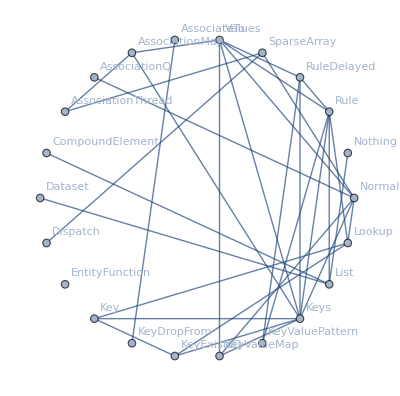
<|attributes→{HoldAllComplete,Protected},common option values→Missing[NotApplicable],date introduced→Day: Wed 9 Jul 2014,date last modified→Day: Wed 2 Mar 2016,dates modified→{Day: Wed 2 Mar 2016},documentation basic examples→{{An association in which key a is associated with value x, key b with value y, etc.:,<|a→x,b→y,c→z|>,<|a→x,b→y,c→z|>,Extract the value associated with key b:,%[b],y},{Convert a list of rules to an association:,Association[{a→x,b→y,c→z}],<|a→x,b→y,c→z|>,Convert an association to a list of rules:,Normal[<|a→x,b→y,c→z|>],{a→x,b→y,c→z}},{Keys are "transparent" for many operations:,Map[f,<|a→4,b→2,c→1,d→5|>],<|a→f[4],b→f[2],c→f[1],d→f[5]|>,Sort[<|a→4,b→2,c→1,d→5|>],<|c→1,b→2,a→4,d→5|>,Select[<|a→4,b→2,c→1,d→5|>,#>3&],<|a→4,d→5|>,Total[<|a→4,b→2,c→1,d→5|>],12,Position gives keys in an association:,Position[<|a→4,b→2,c→1,d→5|>,2],{{Key[b]}}},{Append to an association:,Append[<|a→x,b→y,c→z|>,d→w],<|a→x,b→y,c→z,d→w|>},{Delayed rules can be used to construct associations whose values are stored unevaluated:,<|a:>(Print[z];1),b:>(Print[y];2),c:>(Print[z];3)|>,<|a→(Print[z];1),b→(Print[y];2),c→(Print[z];3)|>,The value in the association is evaluated when it is extracted:,%[b],y,2},{Values in associations can be extracted like parts:,<|a→x,b→y,c→z|>[[Key[b]]],y,If the key in an association is a string, no explicit Key is needed to extract it as a part:,<|a→x,b→y,c→z|>[[b]],y,Numerical part specifications work structurally on associations:,<|a→x,b→y,c→z|>[[2]],y,Lookups in associations interoperate with parts in lists and other expressions:,{<|a→x,b→{y,z}|>}[[1,Key[b],2]],z,The explicit Key can be omitted when the keys are strings:,{<|a→x,b→{y,z}|>}[[1,b,2]],z},{Keys extracts the list of keys:,Keys[<|a→x,b→y,c→z|>],{a,b,c}},{Associations can be modified by resetting values:,assoc=<|a→x,b→y,c→z|>,<|a→x,b→y,c→z|>,assoc[b]=w,w,assoc,<|a→x,b→w,c→z|>}},documentation example counts→{BasicExamples→8,Scope→11,GeneralizationsExtensions→0,Options→0,Applications→0,PropertiesRelations→5,PossibleIssues→2,InteractiveExamples→0,NeatExamples→0},documentation example inputs→{BasicExamples→{{<|a→x,b→y,c→z|>,%[b]},{Association[{a→x,b→y,c→z}],Normal[<|a→x,b→y,c→z|>]},{Map[f,<|a→4,b→2,c→1,d→5|>],Sort[<|a→4,b→2,c→1,d→5|>],Select[<|a→4,b→2,c→1,d→5|>,#>3&],Total[<|a→4,b→2,c→1,d→5|>],Position[<|a→4,b→2,c→1,d→5|>,2]},{Append[<|a→x,b→y,c→z|>,d→w]},{<|a:>(Print[z];1),b:>(Print[y];2),c:>(Print[z];3)|>,%[b]},{<|a→x,b→y,c→z|>[[Key[b]]],<|a→x,b→y,c→z|>[[b]],<|a→x,b→y,c→z|>[[2]],{<|a→x,b→{y,z}|>}[[1,Key[b],2]],{<|a→x,b→{y,z}|>}[[1,b,2]]},{Keys[<|a→x,b→y,c→z|>]},{assoc=<|a→x,b→y,c→z|>,assoc[b]=w,assoc}},Scope→{{assoc=Association[Table[i→i^2,{i,10000}]];,assoc[10000]},{Keys[<|{2,3}→x,-Graphics-→y,<|a→1,b→2|>→z|>]},{<|a→x,b→y,c→z|>[d],Lookup[<|a→x,b→y,c→z|>,d,q]},{MatchQ[<|a→1|>,<|_→_|>],Replace[<|a→1|>,<|a→x_|>→x]},{<|1→2|>/.<|a_→b_|>→{a,b}},{f[<|1→2,3→4|>]/.f[<|a_→b_,___|>]→f[a,b]},{<|1→2,2→3,3→4,5→6|>/.<|___,3→b_,___|>→f[b]},{Cases[{<|1→x|>,<|1→x,2→y|>,<|1→x,2→y,3→z|>},<|_,_|>]},{g[<|k_→v_|>]:=v
g[<|1→2|>],h[<|k_→<|k2_->v2_|>|>]:={k,k2,v2}
h[<|1→<|2→3|>|>]},{MatchQ[<|a→1,b→2,c→3|>,KeyValuePattern[b→2]]},{Replace[<|a→1,b→2,c→3|>,KeyValuePattern[{a→x_,c→y_}]→{x,y}]}},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{{Values[<|a→x,b→y,c→z|>],Keys[<|a→x,b→y,c→z|>]},{Normal[<|a→x,b→y,c→z|>]},{<|a→x,a→xp,b→y,c→z,c→zp|>,Join[<|a→x,b→y,c→z|>,<|a→xp,c→zp|>]},{v=w=<|a→1,b→2|>,v[a]=3,{v,w}},{<||>,Length[%]}},PossibleIssues→{{Level[<|a→x,b→y|>,{1}],Depth[<|a→x,b→y|>],Level[{a→x,b→y},{1}],Depth[{a→x,b→y}]},{ReplacePart[<|x→1,y→2|>,{0}→List],Normal[<|x→1,y→2|>]}},InteractiveExamples→{},NeatExamples→{}},documentation example text→{BasicExamples→{{An association in which key a is associated with value x, key b with value y, etc.:,Extract the value associated with key b:},{Convert a list of rules to an association:,Convert an association to a list of rules:},{Keys are "transparent" for many operations:,Position gives keys in an association:},{Append to an association:},{Delayed rules can be used to construct associations whose values are stored unevaluated:,The value in the association is evaluated when it is extracted:},{Values in associations can be extracted like parts:,If the key in an association is a string, no explicit Key is needed to extract it as a part:,Numerical part specifications work structurally on associations:,Lookups in associations interoperate with parts in lists and other expressions:,The explicit Key can be omitted when the keys are strings:},{Keys extracts the list of keys:},{Associations can be modified by resetting values:}},Scope→{{Associations work with any number of elements:,Extracting values from an association is highly efficient:},{Associations can have arbitrary expressions as keys, including associations:},{Missing elements are represented by Missing:,Lookup allows a default value to be given:},{Associations can be used for pattern matching:},{Extract key and value from an association:},{Replace arguments of a function:},{Pick the rule with the specific key:},{Filter associations with length 2 only:},{Define a function using an Association as an argument:,Use nested associations as a function argument:},{KeyValuePattern lets you match any element in an association:},{KeyValuePattern matches elements that appear anywhere in an association:}},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{{Values extracts values from an association:,Keys extracts keys from an association:},{Normal turns an association into a list of rules:},{Associations keep only the last instance of repeated keys:},{When an association is modified, a new copy is created:,v is modified; w is unchanged:},{Associations can have zero length:}},PossibleIssues→{{Association counts as one level, not two, in structural functions:,Lists of rules are two levels:},{Replacing the head of an Association loses keys:,Extract rules from an Association:}},InteractiveExamples→{},NeatExamples→{}},entity classes→{Wolfram Language atomic functions},eponymous people→{},equal-precedence symbols→Missing[NotApplicable],external links→{Fast Introduction for Programmers: Associations→http://www.wolfram.com/language/fast-introduction-for-programmers/associations/},frequencies of usage→{All→0.000137054,StackExchange→0.000903954,TypicalProductionCode→8.58362×10^-6,WolframAlphaCodebase→3.18182×10^-6,WolframDemonstrations→0.,WolframDocumentation→0.00238214},full version introduced→10,full version last modified→10.4,full versions modified→{10.4},functionality areas→{AssociationSymbols},symbol background→Missing[NotAvailable],keyboard shortcuts→Missing[NotAvailable],link trails→{{guide/WolframRoot,guide/Associations,ref/Association},{guide/WolframRoot,guide/FunctionalProgramming,guide/Associations,ref/Association},{guide/WolframRoot,guide/ListManipulation,guide/Associations,ref/Association}},memberships→{Wolfram Language atomic functions},name→Association,option names→{},options→{},plaintext usage→Association[key1->val1, key2->val2, …] or ∖[LeftAssociation]key1->val1, key2->val2, …∖[RightAssociation] represents an association between keys and values.,precedence ranks→Missing[NotApplicable],ranks of usage→{All→210,StackExchange→104,TypicalProductionCode→1014,WolframAlphaCodebase→661,WolframDemonstrations→4864,WolframDocumentation→33},related entities→Missing[NotAvailable],related guide pages→{Computation with Structured Datasetspaclet:guide/ComputationWithStructuredDatasets,Associationspaclet:guide/Associations,Summary of New Features in 10paclet:guide/SummaryOfNewFeaturesIn100,New in 10.0: Core Language & Structurepaclet:guide/NewIn100CoreLanguageAndStructure,Automated Reportspaclet:guide/AutomatedReports,WDF (Wolfram Data Framework)paclet:guide/WDFWolframDataFramework,Summary of New Features in 10.4paclet:guide/SummaryOfNewFeaturesIn104,New in 10.0: Core Languagepaclet:guide/NewIn100CoreLanguage,Language Overviewpaclet:guide/LanguageOverview,Setting Up Input Interpreterspaclet:guide/InterpretingStrings,Wolfram Language Syntax Characterspaclet:guide/WolframLanguageSyntaxCharacters,Expressionspaclet:guide/Expressions,WDFpaclet:guide/WDF,Database Connectivitypaclet:guide/DatabaseConnectivity,Scientific Data Analysispaclet:guide/ScientificDataAnalysis,Wolfram Data Repositorypaclet:guide/WolframDataRepository},related symbols→{List,Dataset,Normal,AssociationQ,Lookup,KeyExistsQ,Keys,Values,KeyValuePattern,SparseArray,CompoundElement},relationship community graph→-Graphics-,relationship graph→-Graphics-,short notations→{∖[LeftAssociation]…∖[RightAssociation]},subject classifications→Missing[NotAvailable],symbols linking to→{AssociateTo,AssociationMap,AssociationQ,AssociationThread,CompoundElement,Dataset,Dispatch,EntityFunction,Key,KeyDropFrom,Keys,KeyValueMap,KeyValuePattern,List,Lookup,Nothing,Rule,RuleDelayed,SparseArray,Values},symbols using as attribute→{},symbols using as option→{},text strings→{Association[Subscript[key, 1]→Subscript[val, 1],Subscript[key, 2]→Subscript[val, 2],…] or ∖[LeftAssociation]Subscript[key, 1]→Subscript[val, 1],Subscript[key, 2]→Subscript[val, 2],…∖[RightAssociation] 
represents an association between keys and values.,The value associated with a given key can be extracted using assoc[key].,An Association acts like a symbolically indexed list. The value associated with a given key can be extracted by using the part specification Key[key]. If key is a string, Key can be omitted.,If key is not present in assoc, assoc[key] yields Missing["KeyAbsent",key].,Typical list operations (such as Map, Select, and Sort) apply to the values in an association, leaving the keys unchanged.,Association[{Subscript[key, 1]->Subscript[val, 1],…}] gives <|Subscript[key, 1]->Subscript[val, 1],…|>.,If there are multiple elements with the same key, all but the last of these elements are dropped. Merge yields instead a list of values for repeated keys.,Association can be input using the characters ∖[LeftAssociation] and ∖[RightAssociation].,Normal converts an Association to a list of rules.,KeyValuePattern can be used to represent a pattern for associations that include particular elements.,An association in which key a is associated with value x, key b with value y, etc.:,Extract the value associated with key b:,Convert a list of rules to an association:,Convert an association to a list of rules:,Keys are "transparent" for many operations:,Position gives keys in an association:,Append to an association:,Delayed rules can be used to construct associations whose values are stored unevaluated:,The value in the association is evaluated when it is extracted:,Values in associations can be extracted like parts:,If the key in an association is a string, no explicit Key is needed to extract it as a part:,Numerical part specifications work structurally on associations:,Lookups in associations interoperate with parts in lists and other expressions:,The explicit Key can be omitted when the keys are strings:,Keys extracts the list of keys:,Associations can be modified by resetting values:,Associations work with any number of elements:,Extracting values from an association is highly efficient:,Associations can have arbitrary expressions as keys, including associations:,Missing elements are represented by Missing:,Lookup allows a default value to be given:,Associations can be used for pattern matching:,Extract key and value from an association:,Replace arguments of a function:,Pick the rule with the specific key:,Filter associations with length 2 only:,Define a function using an Association as an argument:,Use nested associations as a function argument:,KeyValuePattern lets you match any element in an association:,KeyValuePattern matches elements that appear anywhere in an association:,Values extracts values from an association:,Keys extracts keys from an association:,Normal turns an association into a list of rules:,Associations keep only the last instance of repeated keys:,When an association is modified, a new copy is created:,v is modified; w is unchanged:,Associations can have zero length:,Association counts as one level, not two, in structural functions:,Lists of rules are two levels:,Replacing the head of an Association loses keys:,Extract rules from an Association:},timeline→-Graphics-,timeline events→Interval[{Day: Wed 9 Jul 2014,Day: Wed 2 Mar 2016}]Association,translations→{Simplified Chinese→关联,Traditional Chinese→關聯,French→association,German→Assoziation,Modern Greek→σύνδεσμος κλειδιών-αξιών,Japanese→連想,Korean→연상,Lithuanian→asociacija,Polish→stowarzyszenie,Portuguese→associação,Russian→ассоциация,Spanish→asociación,Ukrainian→асоціація,Vietnamese→sự kết hợp},typeset usage→Association[key_1→val_1,key_2→val_2,…] or ∖[LeftAssociation]key_1→val_1,key_2→val_2,…∖[RightAssociation] represents an association between keys and values.,URL→http://reference.wolfram.com/language/ref/Association.html,version introduced→10,version last modified→10.4,versions modified→{10.4},Wolfram documentation link→Associationpaclet:ref/Association|>

```mathematica
Entity["WolframLanguageSymbol","Association"]["PropertyAssociation"]
```

EntityPropertyAssociation:

```mathematica
EntityValue[
	EntityClass["Country", "GroupOf8"],
	{"Population", "MedianAge", "LandArea"},
	"EntityPropertyAssociation"
]
```

<|Canada→<|Population→35949709 people,MedianAge→39.685 yr,LandArea→3.51102×10^6 mi^2|>,France→<|Population→64457201 people,MedianAge→40.027 yr,LandArea→212345. mi^2|>,Germany→<|Population→81707789 people,MedianAge→44.279 yr,LandArea→134623. mi^2|>,Italy→<|Population→59504212 people,MedianAge→43.294 yr,LandArea→113568. mi^2|>,Japan→<|Population→127974958 people,MedianAge→44.862 yr,LandArea→144689. mi^2|>,Russia→<|Population→143888004 people,MedianAge→38.005 yr,LandArea→1999236083984375/316160658 mi^2|>,United Kingdom→<|Population→65397080 people,MedianAge→39.779 yr,LandArea→93409.7 mi^2|>,United States→<|Population→319929162 people,MedianAge→37.064 yr,LandArea→3.53744×10^6 mi^2|>|>

Dataset:

```mathematica
EntityValue[
	EntityClass["Country", "GroupOf8"],
	{"Population", "MedianAge", "LandArea"},
	"Dataset"
]
```

Dataset[<>]

## Association: Performance

There are a couple of downsides to using Association objects.

Creating Association objects can be slow:

```mathematica
keys=ToString/@Range[10^6];
values=Range[10^6];
assoc = AssociationThread[keys, values];//AbsoluteTiming
```

```mathematica
ByteCount[{keys, values}]
ByteCount[assoc]
```

On the other hand, appending elements to an association is much faster than appending elements to a List object:

```mathematica
makeAssociation[n_]:=Module[{tmp=<||>},
Do[AppendTo[tmp, i->i], {i,n}];
tmp
]
```

Check output:

```mathematica
makeAssociation[10]
```

```mathematica
Needs["GeneralUtilities`"]
BenchmarkPlot[{Range, makeAssociation}, Identity, "IncludeFits"->True]
```

-Graphics-

Recall that the List variation earlier had n^2 timing, corresponding to an O(n) timing for appending a single element. The corresponding time for appending a single element to an association scales as O(log n).

Finally, you have already seen that looking up values associated with a Key is extremely fast.

## Dataset

A simple example of a dataset is formed from an association of associations.

```mathematica
data=Dataset[<|"a"-><|"x"->1,"y"->2,"z"->3|>,"b"-><|"x"->5,"y"->10,"z"->7|>|>]
```

Dataset[<>]

Accessing parts of dataset is basically the same as in lists and association.

```mathematica
data["b"]
```

Dataset[<>]

Wolfram Language also has built-in data in form of dataset.

```mathematica
planets=ExampleData[{"Dataset","Planets"}]
```

```mathematica
planets["Mercury"]["Radius"]
```

```mathematica
Select[planets, #["Radius"]>Quantity[50000,"Kilometers"]&]
```

## Association: Summary

Excellent for quickly retrieving values associated to keys.

Excellent timing performance for inserting, deleting, appending, etc.

Many special functions designed to work with s objects.

Memory usage can be high.